```mathematica
Integrate[-2.601*10^-11*m^-1.9*m,{m,0.01, 1.57*10^12}]
```

-4.1484×10^-9

```mathematica
Sum[4^n,{n,0,N}]-Sum[4^n,{n,0,N-1}]
```

1/3 (1-4^N)+1/3 (-1+4^(1+N))

```mathematica
Simplify[1/3 (1-4^N)+1/3 (-1+4^(1+N))]
```

4^N

```mathematica
Simplify[1/3 (1-4^(1+N))+1/3 (-1+4^(2+N))]
```

4^(1+N)

```mathematica
Simplify[Sum[4^n,{n,0,N-1}]/Sum[4^n,{n,0,N}]]^-1
```

(-1+4^(1+N))/(-1+4^N)

```mathematica
FullSimplify[(-1+4^N)/(-1+4^(1+N))]
```

1/(4+3/(-1+4^N))

```mathematica
Integrate[Sqrt[1-x^2],{x,0,1}]
```

π/4

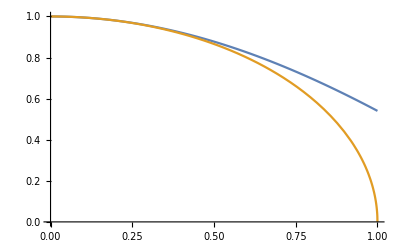

```mathematica
Plot[{Cos[x],Sqrt[1-x^2]},{x,0,1}]
```

```mathematica
N[Integrate[Cos[x]-Sqrt[1-x^2],{x,0,1}]]
```

0.0560728

```mathematica
N[Integrate[Cos[x], {x,0,1}]]
```

0.841471

```mathematica
Dist[x_,D_]:=(2*(1-x)*Sqrt[x*(2-x)]*Cot[D*Pi]+2*x*(2-x))^-0.5
```

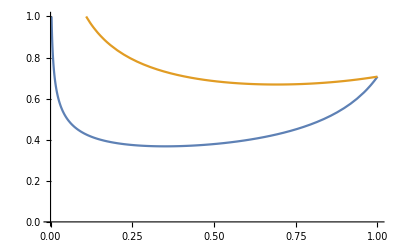

```mathematica
Plot[{Dist[x,0.05],Dist[x,0.3]},{x,0,1},PlotRange->{0,1}]
```

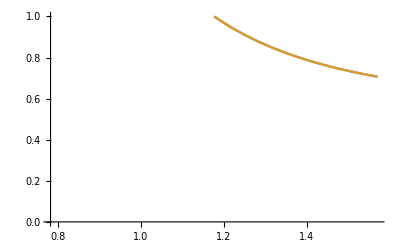

0.000296907

```mathematica
D0 = 0.748755;
D1=0.749770;
Plot[{Dist[1-Cos[x],D0],Dist[1-Cos[x],D1]},{x,0,Pi/2},PlotRange->{0,1}]
NIntegrate[1-Dist[x,D0],{x,1-Cos[Pi/2*D0],1-Cos[Pi/2*D1]}]+NIntegrate[Dist[x,D1]-Dist[x,D0],{x,1-Cos[Pi/2*D1],1}]
```

```mathematica
NumberForm[0.07019212315634205,16]
```

0.07019212315634205

```mathematica
NumberForm[0.009797089074945814,16]
```

0.00979708907494582

```mathematica
N[1-Cos[Pi/2*0.3]]
```

0.108993

```mathematica
Dist[0.1089934758116321,0.3]
```

1.